```mathematica
Лабораторная работа 8
```

```mathematica
Работа с БД
```

```mathematica
Создадим подключение к БД
```

```mathematica
conn= DatabaseReference[<|"Backend" -> "postgres", "Host" -> "localhost", "Port" -> 5432, "Name"->"citytransport", "Username" -> "postgres", "Password" -> "6675"|>]
```

DatabaseReference[…]

```mathematica
Проверим соединение
```

```mathematica
DatabaseConnect[conn]
conn["Connected"]
```

Success[…]

True

```mathematica
conn[{"Username","Port"}]
```

<|Username→postgres,Port→5432|>

```mathematica
bdObject=RelationalDatabase[conn]
(*представляет информацию схемы о реляционной базе данных.*)
(*дает полную схему базы данных,на которую ссылается db*)
```

RelationalDatabase[…]

```mathematica
entity=EntityStore[bdObject]
(*создает хранилище сущностей из схемы внешней базы данных.*)
```

EntityStore[…]

```mathematica
EntityRegister[entity]
(*регистрирует сущности в хранилище сущностей,чтобы к ним можно было получить прямой доступ с помощью Entity.*)
```

{router,dataintro,tranname,indexes,worktime,transport}

```mathematica
EntityValue[ 
	"tranname",
	{"id_tr","name","number"},
	"Dataset"
]
(*дает список значений указанного свойства для каждого из Subscript[entity,i].*)
```

```mathematica
ExternalEvaluate[conn,"SELECT * FROM transport"]
```

```mathematica
DatabaseDisconnect[conn]
```

Success[…]

```mathematica
Wolfram alpha
```

```mathematica
WolframAlpha["size of the sun", "ShortAnswer"]
```

695700 kilometers

```mathematica
Полный результат запроса
```

size of the sun

WolframAlphaQueryResults

```mathematica
Интерпретация данных
```

```mathematica
Entity["City",{"Minsk","Minsk","Belarus"}]
```

Minsk

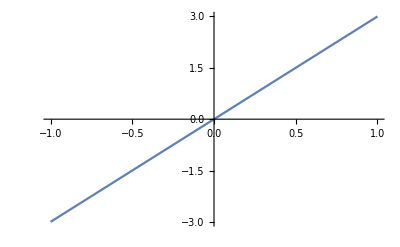

```mathematica
Plot[3*x, {x, -1, 1}] (*==*)
```

WolframAlphaQueryParseResults(*одно =*)

-Graphics-

magenta hex

WolframAlphaQueryResults

red heart

WolframAlphaQueryResults